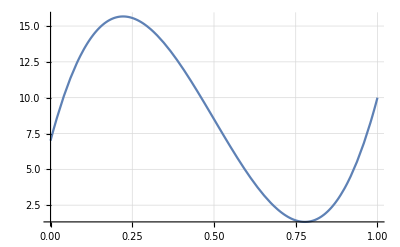

```mathematica
nprob=2;
ngran=1;
Subscript[Q, a]=5;Subscript[Q, b]=4; Subscript[u, a]=7;Subscript[u, b]=10;
a=0; b=1;
λ[x_]:={10+20x(x-1),10}
q[x_]:={10000(x-0.5),-10000(x-0.5)}
Subscript[u, ∞]={{200,300},{300,300}};
α={{10^5,10^2},{10^2,10^2}};
Gran={{u[a]==Subscript[u, a],u[b]==Subscript[u, b]},{(λ[x][[nprob]]/.x->a) u'[a]==Subscript[Q, a],(-λ[x][[nprob]]/.x->b) u'[b]==Subscript[Q, b]},{(λ[x][[nprob]] u'[a]/.x->a)==α[[nprob]][[1]](u[a]-Subscript[u, ∞][[nprob]][[1]]),(-λ[x][[nprob]]/.x->b )u'[b]==α[[nprob]][[2]](u[b]-Subscript[u, ∞][[nprob]][[2]])}};
K={D[λ[x][[nprob]]u'[x],x]+q[x][[nprob]]==0}~Join~Gran[[ngran]];
s=NDSolveValue[K,u,{x,a,b}];
KK=Plot[Evaluate[s[x]], {x, a, b}, PlotRange -> All,GridLines->Automatic]
```

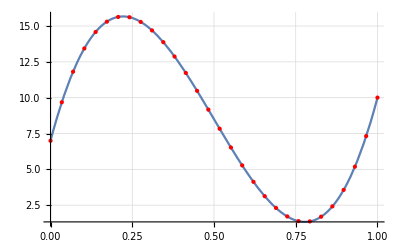

```mathematica
data=Import["D:\\1\\RPC lab\\lab3\\lab3\\outf.txt","Table"];
T=Plot[0,{x,0,1},PlotRange->{{0,1},{100,350}}];
Show[KK,Graphics[{Red,Thick,Table[Point[{data[[i]][[1]],data[[i]][[2]]}],{i,1,Length[data]}]}]]
```

```mathematica
Integrate[(x2-x)/(x2-x1),{x,x1,x2}]
Integrate[(x-x1)/(x2-x1),{x,x1,x2}]
```

x2+x1^2/(2 (-x1+x2))-x2^2/(2 (-x1+x2))

-x1-x1^2/(2 (-x1+x2))+x2^2/(2 (-x1+x2))